```mathematica
SusceptHeight={{4,1.310617,0.00520}, {8, 4.002690545,0.029074},{16,12.953, 0.1056}, {32, 41.5689916, 1.2237},{64,138.6132,14.547}};
SusceptHeightPoints = Table[Log[{SusceptHeight[[i]][[1]],SusceptHeight[[i]][[2]]}], {i, 1, Length[SusceptHeight]}];
SusceptHeightErrors = Table[SusceptHeight[[i]][[3]]/SusceptHeight[[i]][[2]],{i,1,Length[SusceptHeight]}];
SusceptWidth={{4, 0.0541,0.00049}, {8,0.026319, 0.000420}, {16,0.01256, 0.000278},{32, 0.006609, 0.000726},{64,0.003468,0.000542}};
SusceptWidthPoints = Table[Log[{SusceptWidth[[i]][[1]],SusceptWidth[[i]][[2]]}], {i, 1, Length[SusceptWidth]}];
SusceptWidthErrors = Table[SusceptWidth[[i]][[3]]/SusceptWidth[[i]][[2]],{i,1,Length[SusceptWidth]}];
SusceptPos={{4, 0.14014395,0.00029}, {8, 0.166519, 0.000259}, {16,0.1786131974,0.00017583},{32, 0.18383, 0.0003149},{64,0.18670,0.000432}};
SusceptPosPoints = Table[{SusceptPos[[i]][[1]],SusceptPos[[i]][[2]]}, {i, 1, Length[SusceptPos]}];
SusceptPosErrors = Table[SusceptPos[[i]][[3]],{i,1,Length[SusceptPos]}];
Needs["ErrorBarPlots`"]
```

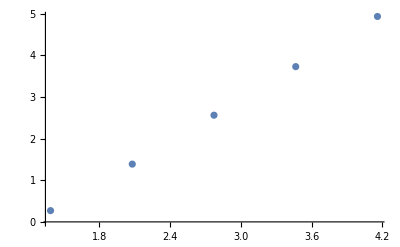

```mathematica
ListPlot[SusceptHeightPoints]
```

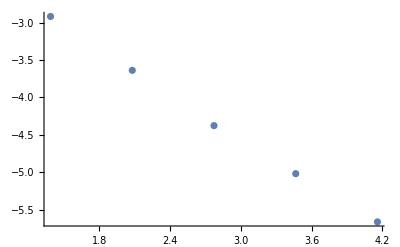

```mathematica
ListPlot[SusceptWidthPoints]
```

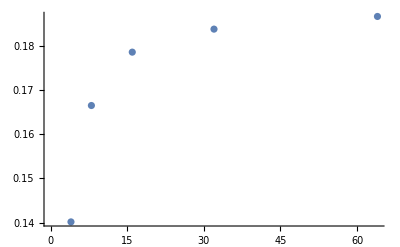

```mathematica
ListPlot[SusceptPosPoints]
```

```mathematica
SusceptHeightFit = NonlinearModelFit[SusceptHeightPoints,(sigmav) x + b, {{sigmav,0.5}, {b,0.5}},x,Weights->1/SusceptHeightErrors^2];
```

```mathematica
SusceptHeightFit[{"BestFit","ParameterTable"}]
```

{-2.01864+1.64854 x, | Estimate | Standard Error | t-Statistic | P-Value
sigmav | 1.64854 | 0.0123437 | 133.553 | 9.25601×10^-7
b | -2.01864 | 0.0227375 | -88.7801 | 3.1501×10^-6}

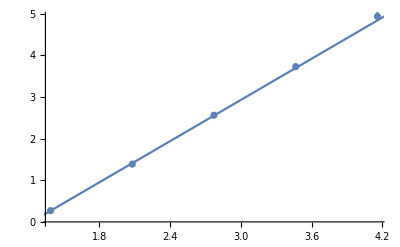

```mathematica
Show[
ErrorListPlot[
Table[{SusceptHeightPoints[[i]][[1]],SusceptHeightPoints[[i]][[2]], SusceptHeightErrors[[i]]},{i,1,Length[SusceptHeightPoints]}]],
Plot[SusceptHeightFit[x],{x,0,5},PlotRange->Full]
]
```

```mathematica
SusceptWidthFit = NonlinearModelFit[SusceptWidthPoints,-(1/v) x + b, {v, b},x,Weights->1/SusceptWidthErrors^2];
```

```mathematica
SusceptWidthFit[{"BestFit","ParameterTable"}]
```

{-1.47014-1.04379 x, | Estimate | Standard Error | t-Statistic | P-Value
v | 0.958049 | 0.0100507 | 95.3219 | 2.54519×10^-6
b | -1.47014 | 0.0194706 | -75.5055 | 5.1199×10^-6}

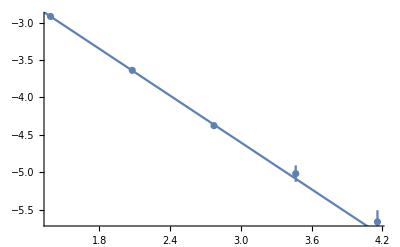

```mathematica
Show[
ErrorListPlot[Table[{SusceptWidthPoints[[i]][[1]],SusceptWidthPoints[[i]][[2]], SusceptWidthErrors[[i]]},{i,1,Length[SusceptWidthPoints]}]],
Plot[SusceptWidthFit[x],{x,0,5},PlotRange->Full]
]
```

```mathematica
SusceptPosFit = NonlinearModelFit[SusceptPosPoints, A*x^(-v) + b, {A,v, b},x,Weights->1/SusceptPosErrors^2];
```

```mathematica
SusceptPosFit[{"BestFit","ParameterTable"}]
```

{0.188599-0.234068/x^1.13605, | Estimate | Standard Error | t-Statistic | P-Value
A | -0.234068 | 0.00454554 | -51.494 | 0.000376913
v | 1.13605 | 0.0163735 | 69.3834 | 0.000207661
b | 0.188599 | 0.000263353 | 716.145 | 1.94983×10^-6}

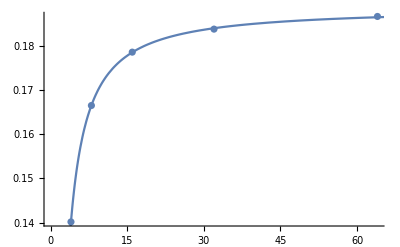

```mathematica
Show[
ErrorListPlot[Table[{SusceptPosPoints[[i]][[1]],SusceptPosPoints[[i]][[2]], SusceptPosErrors[[i]]},{i,1,Length[SusceptPosPoints]}]],
Plot[SusceptPosFit[x],{x,0.1,150},PlotRange->Full]
]
```

```mathematica
MagnetizationHeight = {{8, 0.90404375}, {16,0.841697265625}, {32,0.774832519531}, {64,0.711084960937}, {128, 0.659222839355}};
```

```mathematica
ListPlot[Log[MagnetizationHeight]]
```

ListPlot::lpn: Log[MagnetizationHeight] is not a list of numbers or pairs of numbers.

ListPlot[Log[MagnetizationHeight]]

```mathematica
MagnetizationHeightFit = NonlinearModelFit[Log[MagnetizationHeight],-(betav) x + b, {betav, b},x];
```

```mathematica
MagnetizationHeightFit[{"BestFit","ParameterTable"}]
```

{0.142935-0.115453 x, | Estimate | Standard Error | t-Statistic | P-Value
betav | 0.115453 | 0.00197076 | 58.5831 | 0.0000109572
b | 0.142935 | 0.00709809 | 20.1371 | 0.000267694}

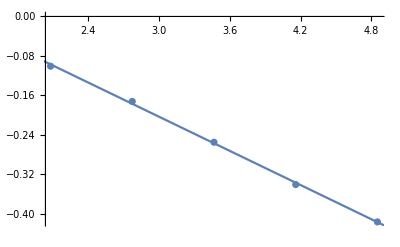

```mathematica
Show[ListPlot[Log[MagnetizationHeight]],Plot[MagnetizationHeightFit[x],{x,0,5}]]
```

```mathematica
MagnetizationHeight = {{8,0.02368}, {16,0.040963}, {32,0.48735}, {64,0.553383}};
```

```mathematica
MagnetizationHeightFit = NonlinearModelFit[Log[MagnetizationHeight],-(betav) x + b, {betav, b},x];
```

```mathematica
MagnetizationHeightFit[{"BestFit","ParameterTable"}]
```

{-7.43093+1.72122 x, | Estimate | Standard Error | t-Statistic | P-Value
betav | -1.72122 | 0.446808 | -3.85225 | 0.0612592
b | -7.43093 | 1.43604 | -5.17461 | 0.0353762}

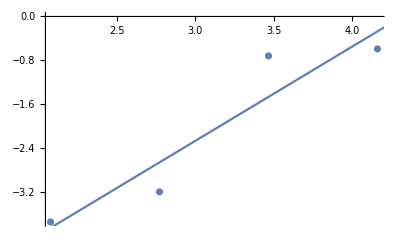

```mathematica
Show[ListPlot[Log[MagnetizationHeight],PlotRange->Full],Plot[MagnetizationHeightFit[x],{x,0,5},PlotRange->Full]]
```